### Tiempo de frenamiento

Aquí en realidad va una suma sobre los b, donde cada b rpresenta una especie del plasma

```mathematica
ν = (ea^2 eb^2)/(4 π ϵ0^2 ma^2 v^3) nb  λab (1+ma/mb)(Erf[v/vsb]-v/vsb Erf'[v/vsb])
```

(ea^2 eb^2 (1+ma/mb) nb λab (-(2 ⅇ^(-v^2/vsb^2) v)/(√π vsb)+Erf[v/vsb]))/(4 ma^2 π v^3 ϵ0^2)

```mathematica
Integrate[1/(ν v), v]
```

(4 ma^2 π ϵ0^2 ∫v^2/(-(2 ⅇ^(-v^2/vsb^2) v)/(√π vsb)+Erf[v/vsb])ⅆv)/(ea^2 eb^2 (1+ma/mb) nb λab)

En primera aproximación supondré que solo hay iones en el plasma

```mathematica
ma = mb
```

mb

```mathematica
ν
```

(ea^2 eb^2 nb λab (-(2 ⅇ^(-v^2/vsb^2) v)/(√π vsb)+Erf[v/vsb]))/(2 mb^2 π v^3 ϵ0^2)

Solo me interesa vsb vsb en función de v para calcular esto

```mathematica
v^2/(-(2 ⅇ^(-v^2/vsb^2) v)/(√π vsb)+Erf[v/vsb])/.v-> x vsb
```

(vsb^2 x^2)/(-(2 ⅇ^(-x^2) x)/(√π)+Erf[x])

```mathematica
int[z_]:=NIntegrate[x^2/(-(2 ⅇ^(-x^2) x)/(√π)+Erf[x]), {x, 1, z}]
```

```mathematica
int[2]
```

2.99209

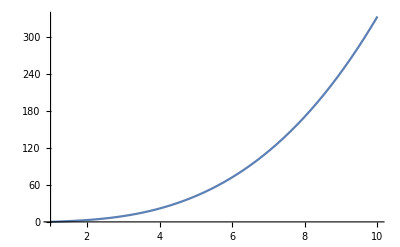

```mathematica
Plot[int[x], {x, 1, 10}]
```

Según el Benchmark la temperatura del plasma es ~2.5 keV y el NBI es de 80 keV de donde v/vsb ~  √(80/2.5)

```mathematica
int[√(80/2.5)]
```

60.7229

Ahora todo lo demás que era

```mathematica
(2 mb^2 π vsb^3 ϵ0^2)/(ea^2 eb^2 nb λab) 60.72
```

(381.515 mb^2 vsb^3 ϵ0^2)/(ea^2 eb^2 nb λab)

```mathematica
mb = 2.014 1.66054 10^-27 ;(* kg*)
kb = 1.380649 10^-23;
e = 1.60217662 10^-19;
ϵ0 = 8.8541878128 10^-12;
vsb = √((2 2.5 10^3 e)/mb);
ea = eb = e;
nb = 0.3 10^20;
λab = 21.125;
```

```mathematica
(2 mb^2 π vsb^3 ϵ0^2)/(ea^2 eb^2 nb λab) 60.72
```

0.0939127

Este último resultado es en segundos

```mathematica
ν
```

(7.57992×10^19 (-2.30552×10^-6 ⅇ^(-4.17473×10^-12 v^2) v+Erf[2.04322×10^-6 v]))/v^3

```mathematica
ν1 = ν + (ea^2 eb^2)/(4 π ϵ0^2 (ma )^2 v^3) nb  17.5 (1+ma/(mb/1836))(Erf[v/(vsb √1830)]-v/(vsb √1830)Erf'[v/(vsb √1830)])
```

(5.76747×10^22 (-5.38944×10^-8 ⅇ^(-2.28127×10^-15 v^2) v+Erf[4.77627×10^-8 v]))/v^3+(7.57992×10^19 (-2.30552×10^-6 ⅇ^(-4.17473×10^-12 v^2) v+Erf[2.04322×10^-6 v]))/v^3

```mathematica
ν
```

(7.57992×10^19 (-2.30552×10^-6 ⅇ^(-4.17473×10^-12 v^2) v+Erf[2.04322×10^-6 v]))/v^3

```mathematica
NIntegrate[1/(ν v), {v, vsb, √(80/2.5)vsb}]
```

0.0939172

```mathematica
NIntegrate[1/(ν1 v), {v, vsb √1830, √(80/2.5)vsb √1830}]
```

9.64986

```mathematica
νe =  (ea^2 eb^2)/(4 π ϵ0^2 (ma )^2 v^3) nb  17.5 (1+ma/(mb/1836))(Erf[v/(vsb √1830)]-v/(vsb √1830)Erf'[v/(vsb √1830)])
```

(5.76747×10^22 (-5.38944×10^-8 ⅇ^(-2.28127×10^-15 v^2) v+Erf[4.77627×10^-8 v]))/v^3

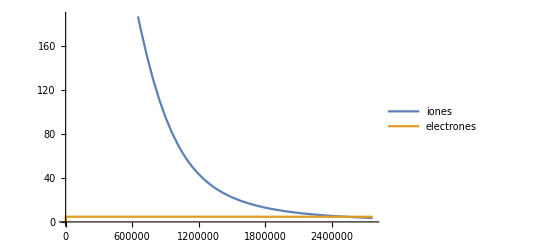

```mathematica
Plot[{ν, νe}, {v, 0, √(80/2.5)vsb}, PlotLegends->{"iones", "electrones"}]
```

```mathematica
NIntegrate[1/(νe v), {v,vsb , √(80/2.5)vsb}]
```

0.367642

```mathematica
NIntegrate[1/(ν v), {v,vsb , √(80/2.5)vsb}]
```

0.0939172

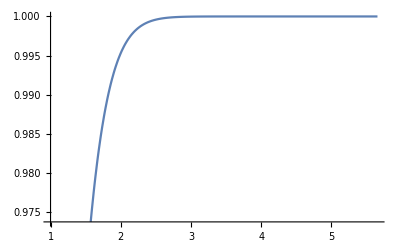

```mathematica
Plot[Erf[x], {x, 1, √(80/2.5)}]
```

## Comprobar resultado del código en C++

```mathematica
ν = (ea^2 eb^2)/(4 π ϵ0^2 ma^2 v^3) nb  λab (1+ma/mb)(Erf[v/vsb]-v/vsb Erf'[v/vsb])
```

(1.01506×10^21 ea^2 eb^2 (1+ma/mb) nb λab (-(2 ⅇ^(-v^2/vsb^2) v)/(√π vsb)+Erf[v/vsb]))/(ma^2 v^3)

```mathematica
e = 1.60217662 10^-19;
ϵ0 = 8.8541878128 10^-12;
me = 9.10938356 10^-31;
```

```mathematica
v0 = 1.84142 10^7;
```

```mathematica
values = {ea->e, eb->e, ma-> 1836 me, nb-> 10^20, λab -> 17.5, mb->me, vsb->1.61029 v0}
```

{ea→1.60218×10^-19,eb→1.60218×10^-19,ma→1.67248×10^-27,nb→100000000000000000000,λab→17.5,mb→9.10938×10^-31,vsb→2.96522×10^7}

```mathematica
ν1 = ν /.values
```

(7.68702×10^23 (-3.80538×10^-8 ⅇ^(-1.13733×10^-15 v^2) v+Erf[3.37243×10^-8 v]))/v^3

```mathematica
NIntegrate[-1/(ν1 v), {v, 0.15v0, 0.037581 v0}]
```

0.0625163

```mathematica
0.67222 * 93
```

62.5165

```mathematica
int[x_]:=NIntegrate[-1/(ν1 v), {v, 0.15v0, x v0}]
```

```mathematica
e^4/(4π ϵ0^2 me^2)
```

806039.

```mathematica
e^4/(4π ϵ0^2 me^2) (10^20 93 10^-3)/((1.84142 10^7)^3)
```

1200.55

```mathematica
1.84142 10^7 93 10^-3/0.5
```

3.42504×10^6

```mathematica
0.103218 * 93 10^-6
```

9.59927×10^-6

Funciona bastante bien, quizás con un paso adaptativo en la integración en el código funcione mejor

### Tiempo de dispersión

```mathematica
(π ϵ0^2 (1836 me)^2 (0.15 1.84142 10^7)^3)/(10^20 e^4 17.5)
```

0.0125899

```mathematica
(4π ϵ0^2 (1836 me)^2 (0.15 1.84142 10^7)^3)/(10^20 e^4 17.5 1837)
```

0.0000274141

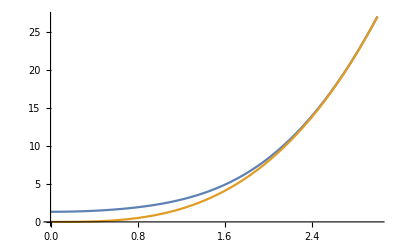

```mathematica
Plot[{x^3/(Erf[x]-x Erf'[x]), x^3}, {x, 0, 3}]
```

```mathematica
((0.001542590 v0 )^2* 1836 me/2)/e
```

4.21141

```mathematica
((1.61029 v0 )^2*  me/2)/e
```

2499.55

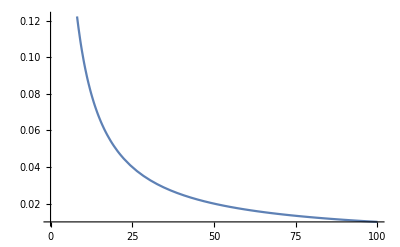

```mathematica
Plot[1/x *(Erf[x]- (Erf[x]-x Erf'[x])/(2 x^2)), {x, 0, 100}]
```

```mathematica
dPerp=e^4/(2π ϵ0^2 (1836 me)^2)10^20 17.5/(v v0)(Erf[v/1.61029]-(Erf[v/1.61029]-v/1.61029 Erf'[v/1.61029])/(2 (v/1.61029)^2));
dPar=e^4/(2π ϵ0^2 (1836 me)^2)10^20 17.5/(v v0)((Erf[v/1.61029]-v/1.61029 Erf'[v/1.61029])/(2 (v/1.61029)^2));
```

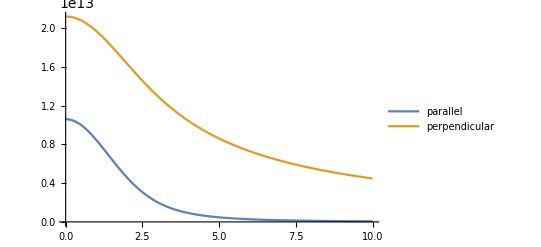

```mathematica
teo = Plot[{dPar, dPerp}, {v, 0, 10} ,PlotLegends->{"parallel", "perpendicular"}]
```

```mathematica
{dPar, dPerp}/.v->2.3
```

{3.61808×10^12,1.5285×10^13}

```mathematica
Δt = 20000 *  0.00001 * 93 10^-3
```

0.0186

```mathematica
τ = 93 10^-3;
```

```mathematica
(5.38 v0^2)/(1000 τ)
```

1.96158×10^13

```mathematica
(1 v0^2)/(1065 τ)
```

3.42352×10^12

```mathematica
eCGS = 4.8032 10^-10;
meCGS= 9.1094 10^-28;
```

```mathematica
((1836 meCGS)^2(0.15 1.84142 10^9)^3)/(4π eCGS^4 17.5 10^14 (1+1836))
```

0.0000274143

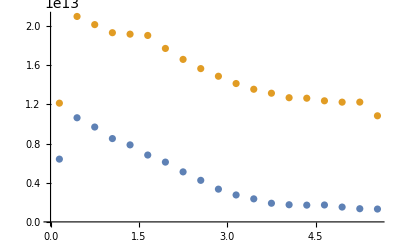

```mathematica
dataSim = Import["/home/michel/Documents/Minimal/build/dispersion_only/cart/process_disp_out.dat"]/.{v_, par_, perp_} -> {v , par * v0^2/Δt, perp * v0^2/Δt};
dataPar = dataSim /. {a_, b_, _}->{a, b};
dataPer = dataSim /. {a_, _, c_}->{a, c};
exp=ListPlot[{dataPar, dataPer}]
```

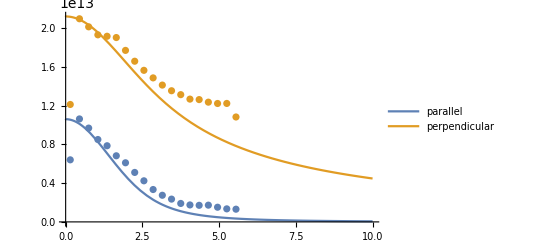

```mathematica
Show[teo, exp]
```

```mathematica
0.00001 93 10^-3
```

9.3×10^-7

```mathematica
ν1/.v-> 0.15 v0
```

22.0643

```mathematica
5 10^12/v0^2
```